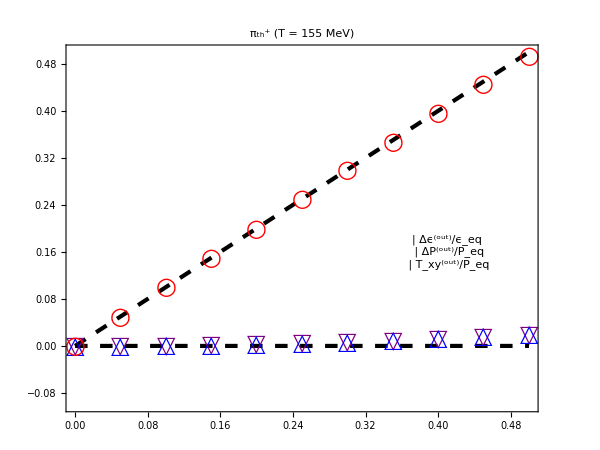

```mathematica
(*PION GAS*)

T0 = 0.155;
mass = 0.140;
sign = 0;
frac=Table[0.05*i,{i,0,10}];


Δϵoverϵdata ={0.0,0.00017913,0.00071662,0.0016127,0.0028679,0.0044827,0.006458,0.0087947,0.011494,0.014557,0.017986};

ΔPoverPeqdata={0.0,0.00019799,0.00079208,0.0017826,0.0031703,0.0049559,0.0071405,0.0097255,0.012713,0.016104,0.019901};

TxyoutoverPeqdata={0.0,0.049993,0.099944,0.14981,0.19955,0.24913,0.29849,0.3476,0.39641,0.44489,0.49297};

style={Directive[RGBColor[0.0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

label=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out)/ϵ_eq",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["ΔP^(out)/P_eq",FontSize->14]},
{Graphics[{Directive[Thick,Red],Circle[]},ImageSize->16],Style["T_xy^(out)/P_eq",FontSize->18]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPoverPeqplot = Table[{frac[[i]],ΔPoverPeqdata[[i]]},{i,1,Length[frac]}];
TxyoutoverPeqplot = Table[{frac[[i]],TxyoutoverPeqdata[[i]]},{i,1,Length[frac]}];


Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΔPoverPeqplot,TxyoutoverPeqplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{○,24}},PlotStyle->{Purple,Blue,Red},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->Inset[label,{0.41,0.16}],ImageSize->{600,500},FrameLabel->{"T_xy^(in)/P_eq"},PlotLabel->Style["π_th^+ (T = 155 MeV)",FontSize->24]]
```

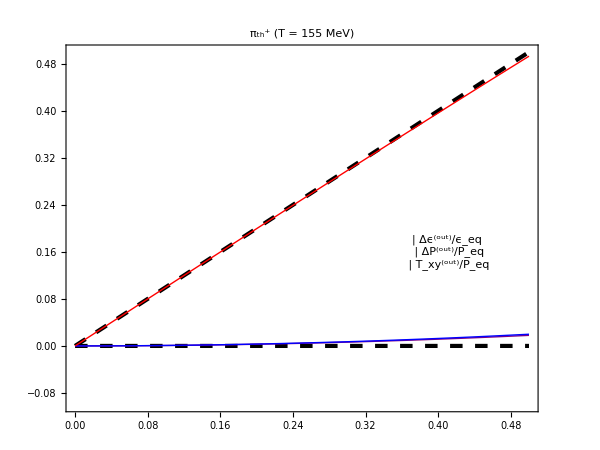

```mathematica
Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListLinePlot[{Δϵoverϵplot,ΔPoverPeqplot,TxyoutoverPeqplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,InterpolationOrder->2,PlotStyle->{Purple,Blue,Red},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->Inset[label,{0.41,0.16}],ImageSize->{600,500},FrameLabel->{"T_xy^(in)/P_eq"},PlotLabel->Style["π_th^+ (T = 155 MeV)",FontSize->24]]
```